```mathematica
tmp=tmpx
tmp=tmp/.CovariantDSlash[a_]->γu[μ].xCovariantD[a,μ]
tmp=MapAt[#/.subD/.tmpD/.Ad[_]->0/.Wud[_,_]->0/.xPartialD[_,_]->0&,tmp,2]
tmp=tmp/.Subscript[P, i_].u Sec[t_](Q Sin[t_]^2-Tu[3])->Subscript[P, i].u Sec[t](Subscript[Q, i] Sin[t]^2-Tud[3,i])
tmp/.RuleX[tmpc,Subscript[Q, i_]]//Simplify
```

ⅈ ū.(𝒟/u)→ⅈ ū.P_L.(𝒟/P_L.u)+ⅈ ū.P_R.(𝒟/P_R.u)

ⅈ ū.γ_μ^μ.(𝔇̲)_μ[u]→ⅈ ū.P_L.γ_μ^μ.(𝔇̲)_μ[P_L.u]+ⅈ ū.P_R.γ_μ^μ.(𝔇̲)_μ[P_R.u]

ⅈ ū.γ_μ^μ.(𝔇̲)_μ[u]→ⅈ ū.P_L.γ_μ^μ.(ⅈ g P_L.u Sec[θw] (Q Sin[θw]^2-T_3^3) Z_(0μ)^(0μ))+ⅈ ū.P_R.γ_μ^μ.(ⅈ g P_R.u Sec[θw] (Q Sin[θw]^2-T_3^3) Z_(0μ)^(0μ))

ⅈ ū.γ_μ^μ.(𝔇̲)_μ[u]→ⅈ ū.P_L.γ_μ^μ.(ⅈ g P_L.u Sec[θw] (Sin[θw]^2 Q_L-T_(3L)^(3L)) Z_(0μ)^(0μ))+ⅈ ū.P_R.γ_μ^μ.(ⅈ g P_R.u Sec[θw] (Sin[θw]^2 Q_R-T_(3R)^(3R)) Z_(0μ)^(0μ))

ⅈ ū.γ_μ^μ.(𝔇̲)_μ[u]→ⅈ (ū.P_L.γ_μ^μ.(ⅈ P_L.u c_L Z_(0μ)^(0μ))+ū.P_R.γ_μ^μ.(ⅈ P_R.u c_R Z_(0μ)^(0μ)))

```mathematica
tmpL//.simpleDot1[{Subscript[c, _]}]
```

ⅈ ū.γ_μ^μ.(𝔇̲)_μ[u]→ⅈ (ⅈ ū.P_L.γ_μ^μ.P_L.u.Z_(0μ)^(0μ) c_L+ⅈ ū.P_R.γ_μ^μ.P_R.u.Z_(0μ)^(0μ) c_R)

```mathematica
tmp=tmpx
tmp//simpleDot3[scalars]
%//.simpleTr2[scalars]//.Dot[a_]:>GammaRight[a,γu[5]]

MM
ExtractPattern[%,Tr[_]][[2,1]]
%//simpleDot3[scalars]
%//.simpleDot
%//.Dot[a___,n_ d_,c___]:>n Dot[a,d,c]/;NumericQ[n]
```

ℳ ℳ^†→-4 G_F^2 (1/2 m_μ (1/2 (1/2 (-1/2 Tr[p_p4^p4.γ_p4^p4.γ_μ^μ.γ_5^5.γ_ν^ν.p_p2^p2.γ_p2^p2.γ_μ^μ.p_p3^p3.γ_p3^p3.γ_ν^ν]-1/2 Tr[p_p4^p4.γ_p4^p4.γ_μ^μ.γ_5^5.γ_ν^ν.p_p2^p2.γ_p2^p2.γ_μ^μ.γ_5^5.p_p3^p3.γ_p3^p3.γ_ν^ν.γ_5^5])+1/2 (-1/2 Tr[p_p4^p4.γ_p4^p4.γ_μ^μ.γ_5^5.γ_ν^ν.γ_5^5.p_p2^p2.γ_p2^p2.γ_μ^μ.p_p3^p3.γ_p3^p3.γ_ν^ν.γ_5^5]-1/2 Tr[p_p4^p4.γ_p4^p4.γ_μ^μ.γ_5^5.γ_ν^ν.γ_5^5.p_p2^p2.γ_p2^p2.γ_μ^μ.γ_5^5.p_p3^p3.γ_p3^p3.γ_ν^ν]))+1/2 (1/2 (-1/2 Tr[p_p4^p4.γ_p4^p4.γ_μ^μ.γ_ν^ν.p_p2^p2.γ_p2^p2.γ_μ^μ.p_p3^p3.γ_p3^p3.γ_ν^ν.γ_5^5]-1/2 Tr[p_p4^p4.γ_p4^p4.γ_μ^μ.γ_ν^ν.p_p2^p2.γ_p2^p2.γ_μ^μ.γ_5^5.p_p3^p3.γ_p3^p3.γ_ν^ν])+1/2 (-1/2 Tr[p_p4^p4.γ_p4^p4.γ_μ^μ.γ_ν^ν.γ_5^5.p_p2^p2.γ_p2^p2.γ_μ^μ.p_p3^p3.γ_p3^p3.γ_ν^ν]-1/2 Tr[p_p4^p4.γ_p4^p4.γ_μ^μ.γ_ν^ν.γ_5^5.p_p2^p2.γ_p2^p2.γ_μ^μ.γ_5^5.p_p3^p3.γ_p3^p3.γ_ν^ν.γ_5^5])))+1/2 (1/2 (1/2 (1/2 Tr[p_p4^p4.γ_p4^p4.γ_μ^μ.p_p1^p1.γ_p1^p1.γ_ν^ν.p_p2^p2.γ_p2^p2.γ_μ^μ.p_p3^p3.γ_p3^p3.γ_ν^ν]+1/2 Tr[p_p4^p4.γ_p4^p4.γ_μ^μ.p_p1^p1.γ_p1^p1.γ_ν^ν.p_p2^p2.γ_p2^p2.γ_μ^μ.γ_5^5.p_p3^p3.γ_p3^p3.γ_ν^ν.γ_5^5])+1/2 (1/2 Tr[p_p4^p4.γ_p4^p4.γ_μ^μ.p_p1^p1.γ_p1^p1.γ_ν^ν.γ_5^5.p_p2^p2.γ_p2^p2.γ_μ^μ.p_p3^p3.γ_p3^p3.γ_ν^ν.γ_5^5]+1/2 Tr[p_p4^p4.γ_p4^p4.γ_μ^μ.p_p1^p1.γ_p1^p1.γ_ν^ν.γ_5^5.p_p2^p2.γ_p2^p2.γ_μ^μ.γ_5^5.p_p3^p3.γ_p3^p3.γ_ν^ν]))+1/2 (1/2 (1/2 Tr[p_p4^p4.γ_p4^p4.γ_μ^μ.γ_5^5.p_p1^p1.γ_p1^p1.γ_ν^ν.p_p2^p2.γ_p2^p2.γ_μ^μ.p_p3^p3.γ_p3^p3.γ_ν^ν.γ_5^5]+1/2 Tr[p_p4^p4.γ_p4^p4.γ_μ^μ.γ_5^5.p_p1^p1.γ_p1^p1.γ_ν^ν.p_p2^p2.γ_p2^p2.γ_μ^μ.γ_5^5.p_p3^p3.γ_p3^p3.γ_ν^ν])+1/2 (1/2 Tr[p_p4^p4.γ_p4^p4.γ_μ^μ.γ_5^5.p_p1^p1.γ_p1^p1.γ_ν^ν.γ_5^5.p_p2^p2.γ_p2^p2.γ_μ^μ.p_p3^p3.γ_p3^p3.γ_ν^ν]+1/2 Tr[p_p4^p4.γ_p4^p4.γ_μ^μ.γ_5^5.p_p1^p1.γ_p1^p1.γ_ν^ν.γ_5^5.p_p2^p2.γ_p2^p2.γ_μ^μ.γ_5^5.p_p3^p3.γ_p3^p3.γ_ν^ν.γ_5^5]))))

ℳ ℳ^†→1/4 G_F^2 m_μ Tr[γ_p4^p4.γ_μ^μ.γ_5^5.γ_ν^ν.γ_p2^p2.γ_μ^μ.γ_p3^p3.γ_ν^ν p_p2^p2 p_p3^p3 p_p4^p4]+1/4 G_F^2 m_μ Tr[γ_p4^p4.γ_μ^μ.γ_ν^ν.γ_5^5.γ_p2^p2.γ_μ^μ.γ_p3^p3.γ_ν^ν p_p2^p2 p_p3^p3 p_p4^p4]+1/4 G_F^2 m_μ Tr[γ_p4^p4.γ_μ^μ.γ_ν^ν.γ_p2^p2.γ_μ^μ.γ_5^5.γ_p3^p3.γ_ν^ν p_p2^p2 p_p3^p3 p_p4^p4]+1/4 G_F^2 m_μ Tr[γ_p4^p4.γ_μ^μ.γ_ν^ν.γ_p2^p2.γ_μ^μ.γ_p3^p3.γ_ν^ν.γ_5^5 p_p2^p2 p_p3^p3 p_p4^p4]+1/4 G_F^2 m_μ Tr[γ_p4^p4.γ_μ^μ.γ_5^5.γ_ν^ν.γ_5^5.γ_p2^p2.γ_μ^μ.γ_5^5.γ_p3^p3.γ_ν^ν p_p2^p2 p_p3^p3 p_p4^p4]+1/4 G_F^2 m_μ Tr[γ_p4^p4.γ_μ^μ.γ_5^5.γ_ν^ν.γ_5^5.γ_p2^p2.γ_μ^μ.γ_p3^p3.γ_ν^ν.γ_5^5 p_p2^p2 p_p3^p3 p_p4^p4]+1/4 G_F^2 m_μ Tr[γ_p4^p4.γ_μ^μ.γ_5^5.γ_ν^ν.γ_p2^p2.γ_μ^μ.γ_5^5.γ_p3^p3.γ_ν^ν.γ_5^5 p_p2^p2 p_p3^p3 p_p4^p4]+1/4 G_F^2 m_μ Tr[γ_p4^p4.γ_μ^μ.γ_ν^ν.γ_5^5.γ_p2^p2.γ_μ^μ.γ_5^5.γ_p3^p3.γ_ν^ν.γ_5^5 p_p2^p2 p_p3^p3 p_p4^p4]-1/4 G_F^2 Tr[γ_p4^p4.γ_μ^μ.γ_p1^p1.γ_ν^ν.γ_p2^p2.γ_μ^μ.γ_p3^p3.γ_ν^ν p_p1^p1 p_p2^p2 p_p3^p3 p_p4^p4]-1/4 G_F^2 Tr[γ_p4^p4.γ_μ^μ.γ_5^5.γ_p1^p1.γ_ν^ν.γ_5^5.γ_p2^p2.γ_μ^μ.γ_p3^p3.γ_ν^ν p_p1^p1 p_p2^p2 p_p3^p3 p_p4^p4]-1/4 G_F^2 Tr[γ_p4^p4.γ_μ^μ.γ_5^5.γ_p1^p1.γ_ν^ν.γ_p2^p2.γ_μ^μ.γ_5^5.γ_p3^p3.γ_ν^ν p_p1^p1 p_p2^p2 p_p3^p3 p_p4^p4]-1/4 G_F^2 Tr[γ_p4^p4.γ_μ^μ.γ_5^5.γ_p1^p1.γ_ν^ν.γ_p2^p2.γ_μ^μ.γ_p3^p3.γ_ν^ν.γ_5^5 p_p1^p1 p_p2^p2 p_p3^p3 p_p4^p4]-1/4 G_F^2 Tr[γ_p4^p4.γ_μ^μ.γ_p1^p1.γ_ν^ν.γ_5^5.γ_p2^p2.γ_μ^μ.γ_5^5.γ_p3^p3.γ_ν^ν p_p1^p1 p_p2^p2 p_p3^p3 p_p4^p4]-1/4 G_F^2 Tr[γ_p4^p4.γ_μ^μ.γ_p1^p1.γ_ν^ν.γ_5^5.γ_p2^p2.γ_μ^μ.γ_p3^p3.γ_ν^ν.γ_5^5 p_p1^p1 p_p2^p2 p_p3^p3 p_p4^p4]-1/4 G_F^2 Tr[γ_p4^p4.γ_μ^μ.γ_p1^p1.γ_ν^ν.γ_p2^p2.γ_μ^μ.γ_5^5.γ_p3^p3.γ_ν^ν.γ_5^5 p_p1^p1 p_p2^p2 p_p3^p3 p_p4^p4]-1/4 G_F^2 Tr[γ_p4^p4.γ_μ^μ.γ_5^5.γ_p1^p1.γ_ν^ν.γ_5^5.γ_p2^p2.γ_μ^μ.γ_5^5.γ_p3^p3.γ_ν^ν.γ_5^5 p_p1^p1 p_p2^p2 p_p3^p3 p_p4^p4]

ℳ ℳ^†→-2 G_F^2 p_p1^p1 p_p2^p2 p_p3^p3 p_p4^p4 Tr[γ_p4^p4.γ_μ^μ.γ_p1^p1.γ_ν^ν.γ_p2^p2.γ_μ^μ.γ_p3^p3.γ_ν^ν]+G_F^2 m_μ p_p2^p2 p_p3^p3 p_p4^p4 Tr[-γ_p4^p4.γ_μ^μ.γ_ν^ν.γ_p2^p2.γ_μ^μ.γ_p3^p3.γ_ν^ν.γ_5^5]+G_F^2 m_μ p_p2^p2 p_p3^p3 p_p4^p4 Tr[γ_p4^p4.γ_μ^μ.γ_ν^ν.γ_p2^p2.γ_μ^μ.γ_p3^p3.γ_ν^ν.γ_5^5]

MM

{}⟦2,1⟧

{}⟦2,1⟧

{}⟦2,1⟧

«1 more identical outputs»

```mathematica
NumericQ[-I]
Dot[a,Dot[d b,c]]
simpleDot
```

True

a.(b d).c

{a___.(d_ n_).c___:>n a.d.c/;NumericQ[n],a___.b_.c___:>b a.c/;NumericQ[b],a___.(-b_).c___→-a.b.c}

```mathematica
tmpD
ExtractPattern[tmpD, Zud[0,μ]]
```

(𝔇̲)_μ[φ]→-ⅈ g Q φ Sin[θw] A_μ^μ-(ⅈ g φ T_-^- W_-μ^-μ)/(√2)-(ⅈ g φ T_+^+ W_(+μ)^(+μ))/(√2)+ⅈ g φ Sec[θw] (Q Sin[θw]^2-T_3^3) Z_(0μ)^(0μ)+UnderBar[∂]_μ[φ]

{}

```mathematica
tmpx
%//simpleDot3[{pdd[_,_]}]
%//.simpleTr2[{pdd[_,_]}]
%/.subTraceGamma0
%//Expand
%//MetricSimplify[g]
```

Tr[(p_uα^uα γ_α^α).γ_ν^ν.(p_vβ^vβ γ_β^β).γ_μ^μ.(1/2 (1-γ_5^5))]

Tr[1/2 γ_α^α.γ_ν^ν.γ_β^β.γ_μ^μ p_uα^uα p_vβ^vβ-1/2 γ_α^α.γ_ν^ν.γ_β^β.γ_μ^μ.γ_5^5 p_uα^uα p_vβ^vβ]

1/2 p_uα^uα p_vβ^vβ Tr[γ_α^α.γ_ν^ν.γ_β^β.γ_μ^μ]-1/2 p_uα^uα p_vβ^vβ Tr[γ_α^α.γ_ν^ν.γ_β^β.γ_μ^μ.γ_5^5]

2 (g_αν^αν g_βμ^βμ+g_αμ^αμ g_νβ^νβ-g_αβ^αβ g_νμ^νμ) p_uα^uα p_vβ^vβ+2 ⅈ p_uα^uα p_vβ^vβ ϵ_ανβμ^ανβμ

2 g_αν^αν g_βμ^βμ p_uα^uα p_vβ^vβ+2 g_αμ^αμ g_νβ^νβ p_uα^uα p_vβ^vβ-2 g_αβ^αβ g_νμ^νμ p_uα^uα p_vβ^vβ+2 ⅈ p_uα^uα p_vβ^vβ ϵ_ανβμ^ανβμ

-2 g_νμ^νμ p_vβ^vβ p_uβ^uβ+2 p_vμ^vμ p_uν^uν+2 p_uμ^uμ p_vν^vν+2 ⅈ p_uα^uα p_vβ^vβ ϵ_ανβμ^ανβμ

```mathematica
tmp=tmpx
tmp=tmp//.subTraceGamma0
tmp=tmp(-gdd[ν,μ]+qd[ν]qd[μ]/Subscript[M, z]^2)//Expand
%/.ϵuuuu[_,_,_,_]->0
%//MetricSimplify[g]
```

1/2 p_uα^uα p_vβ^vβ Tr[γ_α^α.γ_ν^ν.γ_β^β.γ_μ^μ]-1/2 p_uα^uα p_vβ^vβ Tr[γ_α^α.γ_ν^ν.γ_β^β.γ_μ^μ.γ_5^5]

2 (g_αν^αν g_βμ^βμ+g_αμ^αμ g_νβ^νβ-g_αβ^αβ g_νμ^νμ) p_uα^uα p_vβ^vβ+2 ⅈ p_uα^uα p_vβ^vβ ϵ_ανβμ^ανβμ

-2 g_νμ^νμ g_αν^αν g_βμ^βμ p_uα^uα p_vβ^vβ-2 g_νμ^νμ g_αμ^αμ g_νβ^νβ p_uα^uα p_vβ^vβ+2 g_νμ^νμ g_αβ^αβ g_νμ^νμ p_uα^uα p_vβ^vβ+(2 g_αν^αν g_βμ^βμ p_uα^uα p_vβ^vβ q_μ^μ q_ν^ν)/M_z^2+(2 g_αμ^αμ g_νβ^νβ p_uα^uα p_vβ^vβ q_μ^μ q_ν^ν)/M_z^2-(2 g_αβ^αβ g_νμ^νμ p_uα^uα p_vβ^vβ q_μ^μ q_ν^ν)/M_z^2-2 ⅈ g_νμ^νμ p_uα^uα p_vβ^vβ ϵ_ανβμ^ανβμ+(2 ⅈ p_uα^uα p_vβ^vβ q_μ^μ q_ν^ν ϵ_ανβμ^ανβμ)/M_z^2

-2 g_νμ^νμ g_αν^αν g_βμ^βμ p_uα^uα p_vβ^vβ-2 g_νμ^νμ g_αμ^αμ g_νβ^νβ p_uα^uα p_vβ^vβ+2 g_νμ^νμ g_αβ^αβ g_νμ^νμ p_uα^uα p_vβ^vβ+(2 g_αν^αν g_βμ^βμ p_uα^uα p_vβ^vβ q_μ^μ q_ν^ν)/M_z^2+(2 g_αμ^αμ g_νβ^νβ p_uα^uα p_vβ^vβ q_μ^μ q_ν^ν)/M_z^2-(2 g_αβ^αβ g_νμ^νμ p_uα^uα p_vβ^vβ q_μ^μ q_ν^ν)/M_z^2

-4 p_vβ^vβ p_uβ^uβ+2 g_νν^νν p_vβ^vβ p_uβ^uβ+(2 p_vμ^vμ p_uν^uν q_μ^μ q_ν^ν)/M_z^2+(2 p_uμ^uμ p_vν^vν q_μ^μ q_ν^ν)/M_z^2-(2 p_vβ^vβ p_uβ^uβ q_ν^ν q_ν^ν)/M_z^2

```mathematica
(-gdd[ν,μ]+qd[ν]qd[μ]/Subscript[M, z]^2)/.subq//Expand
tmpx
```

-g_νμ^νμ+(p_uμ^uμ p_uν^uν)/M_z^2+(p_uν^uν p_vμ^vμ)/M_z^2+(p_uμ^uμ p_vν^vν)/M_z^2+(p_vμ^vμ p_vν^vν)/M_z^2

1/2 p_uα^uα p_vβ^vβ Tr[γ_α^α.γ_ν^ν.γ_β^β.γ_μ^μ]-1/2 p_uα^uα p_vβ^vβ Tr[γ_α^α.γ_ν^ν.γ_β^β.γ_μ^μ.γ_5^5]

```mathematica
ParticleData["GaugeBoson","Properties"]
ParticleData["GaugeBoson","FullSymbol"]
ParticleData["GaugeBoson","Parity"]
```

{Antiparticle,BaryonNumber,Bottomness,Charge,ChargeStates,Charm,CParity,DecayModes,DecayType,Excitations,FullDecayModes,FullSymbol,GenericFullSymbol,GenericSymbol,GFactor,GParity,HalfLife,Hypercharge,Isospin,IsospinMultiplet,IsospinProjection,LeptonNumber,Lifetime,Mass,MeanSquareChargeRadius,Memberships,Parity,PDGNumber,QuarkContent,Spin,Strangeness,Symbol,Topness,UnobservedDecayModes,Width}

{g,γ,W^-,W^+,Z}

{Missing[NotAvailable],-1,Missing[NotApplicable],Missing[NotApplicable],Missing[NotApplicable]}

```mathematica
"Starting with the above ovariant derivative"
sub=MapAt[#/.φ->φ_&,tmpD,{1}]
"The amplitude: "
tmpM0
tmp=MapAt[#/.sub//.DotExpand&,tmpM0,{2}]//simpleDot3[{}];
"Isolate the W+ boson interaction term: "
tmp=tmp/.Wud["-",_]->0/.Zud[0,_]->0/.Ad[_]->0/.Subscript[P, R].v->0//PartialDSimplify[{Subscript[P, _]}];
tmp=tmp//simpleDot3[{g}]//Last//Last
```

Starting with the above ovariant derivative

(𝔇̲)_μ[φ_]→-ⅈ g Q φ Sin[θw] A_μ^μ-(ⅈ g φ T_-^- W_-μ^-μ)/(√2)-(ⅈ g φ T_+^+ W_(+μ)^(+μ))/(√2)+ⅈ g φ Sec[θw] (Q Sin[θw]^2-T_3^3) Z_(0μ)^(0μ)+UnderBar[∂]_μ[φ]

The amplitude:

ⅈ ū.γ_μ^μ.(𝔇̲)_μ[v]→ⅈ ū.P_L.γ_μ^μ.(𝔇̲)_μ[P_L.v]+ⅈ ū.P_R.γ_μ^μ.(𝔇̲)_μ[P_R.v]

Isolate the W+ boson interaction term:

(g ū.P_L.γ_μ^μ.P_L.v.T_+^+.W_(+μ)^(+μ))/(√2)

```mathematica
tmpM0
```

ⅈ ū.γ_μ^μ.(𝔇̲)_μ[v]→ⅈ ū.P_L.γ_μ^μ.(𝔇̲)_μ[P_L.v]+ⅈ ū.P_R.γ_μ^μ.(𝔇̲)_μ[P_R.v]

```mathematica
MatrixForm[K1={{0,1,0,0},{1,0,0,0},{0,0,0,0},{0,0,0,0}}
]
```

(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
xtmp//Expand;
%/.ϵuuuu[0,_,_,0]->0/.ϵuduu[_,a_,_,a_]->0/.qd[a_]qd[b_]ϵuuuu[_,a_,_,b_]->0/.gdd[a_,b_]ϵuuuu[_,a_,_,b_]->0;
%//MetricContractG;
%/.ϵuduu[_,a_,_,a_]->0/.ϵuuuu[0,_,_,0]->0
%/.guu[0,0]->1/.gdu[a_,a_]->-2/.qu[0]->Subscript[M, W]/.qu[a_]qd[a_]->Subscript[M, W]^2;
MapAt[SimplifyTensorSum,%,{2}];
%/.subq//Expand
%/.pdd[c_,a_]pdd[c_,b_]ϵuuuu[_,_,a_,b_]->0/.pdd[c_,a_]pdd[c_,b_]ϵuuuu[_,a_,_,b_]->0
```

ℳ[ϵ_ν^ν]^†.ℳ[ϵ_μ^μ]→-4 g^2 p_u0^u0 p_v0^v0+g^2 p_uB^uB p_vB^vB+2 g^2 g_00^00 p_uB^uB p_vB^vB-g^2 g_μμ^μμ p_uB^uB p_vB^vB+g^2 p_vν^vν p_uν^uν-(2 g^2 p_uB^uB p_vB^vB (q_0^0)^2)/M_W^2+(2 g^2 p_v0^v0 p_uμ^uμ q_0^0 q_μ^μ)/M_W^2+(2 g^2 p_u0^u0 p_vμ^vμ q_0^0 q_μ^μ)/M_W^2-(g^2 p_vμ^vμ p_uν^uν q_μ^μ q_ν^ν)/M_W^2-(g^2 p_uμ^uμ p_vν^vν q_μ^μ q_ν^ν)/M_W^2+(g^2 p_uB^uB p_vB^vB q_ν^ν q_ν^ν)/M_W^2-(2 ⅈ g^2 p_uA^uA p_vB^vB q_0^0 q_μ^μ ϵ_(0BAμ)^(0BAμ))/M_W^2

ℳ[ϵ_ν^ν]^†.ℳ[ϵ_μ^μ]→-4 g^2 p_u0^u0 p_v0^v0+(2 g^2 p_v0^v0 p_uB^uB p_uB^uB)/M_W+(2 g^2 p_u0^u0 p_vB^vB p_uB^uB)/M_W+5 g^2 p_uB^uB p_vB^vB+(2 g^2 p_v0^v0 p_uB^uB p_vB^vB)/M_W+(2 g^2 p_u0^u0 p_vB^vB p_vB^vB)/M_W-(g^2 p_vB^vB p_uB^uB p_uν^uν p_uν^uν)/M_W^2-(g^2 p_vB^vB p_uν^uν p_vB^vB p_uν^uν)/M_W^2-(g^2 p_vB^vB p_uB^uB p_vν^vν p_uν^uν)/M_W^2-(g^2 p_vB^vB p_vB^vB p_vν^vν p_uν^uν)/M_W^2-(g^2 p_uB^uB p_uB^uB p_uν^uν p_vν^vν)/M_W^2-(g^2 p_uB^uB p_uν^uν p_vB^vB p_vν^vν)/M_W^2-(g^2 p_uB^uB p_uB^uB p_vν^vν p_vν^vν)/M_W^2-(g^2 p_uB^uB p_vB^vB p_vν^vν p_vν^vν)/M_W^2-(2 ⅈ g^2 p_uB^uB p_uμ^uμ p_vν^vν ϵ_(0νBμ)^(0νBμ))/M_W-(2 ⅈ g^2 p_uB^uB p_vμ^vμ p_vν^vν ϵ_(0νBμ)^(0νBμ))/M_W

ℳ[ϵ_ν^ν]^†.ℳ[ϵ_μ^μ]→-4 g^2 p_u0^u0 p_v0^v0+(2 g^2 p_v0^v0 p_uB^uB p_uB^uB)/M_W+(2 g^2 p_u0^u0 p_vB^vB p_uB^uB)/M_W+5 g^2 p_uB^uB p_vB^vB+(2 g^2 p_v0^v0 p_uB^uB p_vB^vB)/M_W+(2 g^2 p_u0^u0 p_vB^vB p_vB^vB)/M_W-(g^2 p_vB^vB p_uB^uB p_uν^uν p_uν^uν)/M_W^2-(g^2 p_vB^vB p_uν^uν p_vB^vB p_uν^uν)/M_W^2-(g^2 p_vB^vB p_uB^uB p_vν^vν p_uν^uν)/M_W^2-(g^2 p_vB^vB p_vB^vB p_vν^vν p_uν^uν)/M_W^2-(g^2 p_uB^uB p_uB^uB p_uν^uν p_vν^vν)/M_W^2-(g^2 p_uB^uB p_uν^uν p_vB^vB p_vν^vν)/M_W^2-(g^2 p_uB^uB p_uB^uB p_vν^vν p_vν^vν)/M_W^2-(g^2 p_uB^uB p_vB^vB p_vν^vν p_vν^vν)/M_W^2

```mathematica
TensorSymmetry[g,2]=Symmetric[1,2]
TensorSymmetry[ϵ,4]=AntiSymmetric[1,2,3,4]
```

Symmetric[1,2]

AntiSymmetric[1,2,3,4]

```mathematica
tmpx//Last;
tmp1=Tr[%]//.simpleTr2[{m,g,ϵd[_],pdd[_,_],guu[_,_]}];
tmp=ExtractPositionPattern[tmp1,Tr[__]]
sub=tmp/.Subscript[P, L]->(1-γu[5])/2//.simpleTr2[{}]/.subTraceGamma0;
tmp=ReplacePart[tmp1,sub]
tmp=tmp//Expand;
tmp=tmp//SymmetrizeSlots[];
tmp=tmp/.ϵd[b_]ϵd[c_]ϵuuuu[_,_,b_,c_]->0
tmp=tmp/.ϵd[a_]ϵd[b_]->-gdd[a,b]+qd[a]qd[b]/Subscript[M, W]^2//Expand

tmp=tmp//MetricContractG
tmp=tmp//SymmetrizeSlots[]
```

{{1,9}→Tr[γ_A^A.γ_μ^μ.P_L],{2,7}→Tr[γ_0^0.γ_A^A.γ_μ^μ.P_L],{3,7}→Tr[γ_ν^ν.γ_A^A.γ_μ^μ.P_L],{4,8}→Tr[γ_0^0.γ_B^B.γ_A^A.γ_μ^μ.P_L],{5,7}→Tr[γ_B^B.γ_ν^ν.γ_A^A.γ_μ^μ.P_L]}

4 g^2 g_Aμ^Aμ g_B0^B0 g_ν0^ν0 p_uA^uA p_vB^vB ϵ_μ^μ ϵ_ν^ν-1/2 g^2 g_ν0^ν0 p_uA^uA p_vB^vB ϵ_μ^μ ϵ_ν^ν (4 (g_(0B)^(0B) g_Aμ^Aμ+g_(0μ)^(0μ) g_BA^BA-g_(0A)^(0A) g_Bμ^Bμ)+4 ⅈ ϵ_(0BAμ)^(0BAμ))-1/4 g^2 p_uA^uA p_vB^vB ϵ_μ^μ ϵ_ν^ν (4 (g_Aμ^Aμ g_Bν^Bν+g_Bμ^Bμ g_νA^νA-g_BA^BA g_νμ^νμ)+4 ⅈ ϵ_BνAμ^BνAμ)

-2 g^2 g_(0μ)^(0μ) g_(0ν)^(0ν) g_AB^AB p_uA^uA p_vB^vB ϵ_μ^μ ϵ_ν^ν+2 g^2 g_(0B)^(0B) g_(0ν)^(0ν) g_Aμ^Aμ p_uA^uA p_vB^vB ϵ_μ^μ ϵ_ν^ν+2 g^2 g_(0A)^(0A) g_(0ν)^(0ν) g_Bμ^Bμ p_uA^uA p_vB^vB ϵ_μ^μ ϵ_ν^ν-g^2 g_Aν^Aν g_Bμ^Bμ p_uA^uA p_vB^vB ϵ_μ^μ ϵ_ν^ν-g^2 g_Aμ^Aμ g_Bν^Bν p_uA^uA p_vB^vB ϵ_μ^μ ϵ_ν^ν+g^2 g_AB^AB g_μν^μν p_uA^uA p_vB^vB ϵ_μ^μ ϵ_ν^ν+2 ⅈ g^2 g_(0ν)^(0ν) p_uA^uA p_vB^vB ϵ_μ^μ ϵ_ν^ν ϵ_(0ABμ)^(0ABμ)

2 g^2 g_(0μ)^(0μ) g_(0ν)^(0ν) g_AB^AB g_μν^μν p_uA^uA p_vB^vB-2 g^2 g_(0B)^(0B) g_(0ν)^(0ν) g_Aμ^Aμ g_μν^μν p_uA^uA p_vB^vB-2 g^2 g_(0A)^(0A) g_(0ν)^(0ν) g_Bμ^Bμ g_μν^μν p_uA^uA p_vB^vB+g^2 g_Aν^Aν g_Bμ^Bμ g_μν^μν p_uA^uA p_vB^vB+g^2 g_Aμ^Aμ g_Bν^Bν g_μν^μν p_uA^uA p_vB^vB-g^2 g_AB^AB g_μν^μν g_μν^μν p_uA^uA p_vB^vB-(2 g^2 g_(0μ)^(0μ) g_(0ν)^(0ν) g_AB^AB p_uA^uA p_vB^vB q_μ^μ q_ν^ν)/M_W^2+(2 g^2 g_(0B)^(0B) g_(0ν)^(0ν) g_Aμ^Aμ p_uA^uA p_vB^vB q_μ^μ q_ν^ν)/M_W^2+(2 g^2 g_(0A)^(0A) g_(0ν)^(0ν) g_Bμ^Bμ p_uA^uA p_vB^vB q_μ^μ q_ν^ν)/M_W^2-(g^2 g_Aν^Aν g_Bμ^Bμ p_uA^uA p_vB^vB q_μ^μ q_ν^ν)/M_W^2-(g^2 g_Aμ^Aμ g_Bν^Bν p_uA^uA p_vB^vB q_μ^μ q_ν^ν)/M_W^2+(g^2 g_AB^AB g_μν^μν p_uA^uA p_vB^vB q_μ^μ q_ν^ν)/M_W^2-2 ⅈ g^2 g_(0ν)^(0ν) g_μν^μν p_uA^uA p_vB^vB ϵ_(0ABμ)^(0ABμ)+(2 ⅈ g^2 g_(0ν)^(0ν) p_uA^uA p_vB^vB q_μ^μ q_ν^ν ϵ_(0ABμ)^(0ABμ))/M_W^2

-4 g^2 p_u0^u0 p_v0^v0+2 g^2 p_uB^uB p_vB^vB+2 g^2 g_00^00 p_uB^uB p_vB^vB-g^2 g_μμ^μμ p_uB^uB p_vB^vB-(2 g^2 p_uB^uB p_vB^vB (q_0^0)^2)/M_W^2+(2 g^2 p_v0^v0 p_uμ^uμ q_0^0 q_μ^μ)/M_W^2+(2 g^2 p_u0^u0 p_vμ^vμ q_0^0 q_μ^μ)/M_W^2-(g^2 p_vμ^vμ p_uν^uν q_μ^μ q_ν^ν)/M_W^2-(g^2 p_uμ^uμ p_vν^vν q_μ^μ q_ν^ν)/M_W^2+(g^2 p_uB^uB p_vB^vB q_ν^ν q_ν^ν)/M_W^2-2 ⅈ g^2 p_uA^uA p_vB^vB ϵ_(0AB0)^(0AB0)+(2 ⅈ g^2 p_uA^uA p_vB^vB q_0^0 q_μ^μ ϵ_(0ABμ)^(0ABμ))/M_W^2

-4 g^2 p_u0^u0 p_v0^v0+2 g^2 p_uB^uB p_vB^vB+2 g^2 g_00^00 p_uB^uB p_vB^vB-g^2 g_μμ^μμ p_uB^uB p_vB^vB-(2 g^2 p_uB^uB p_vB^vB (q_0^0)^2)/M_W^2+(2 g^2 p_v0^v0 p_uμ^uμ q_0^0 q_μ^μ)/M_W^2+(2 g^2 p_u0^u0 p_vμ^vμ q_0^0 q_μ^μ)/M_W^2-(g^2 p_vμ^vμ p_uν^uν q_μ^μ q_ν^ν)/M_W^2-(g^2 p_uμ^uμ p_vν^vν q_μ^μ q_ν^ν)/M_W^2+(g^2 p_uB^uB p_vB^vB q_ν^ν q_ν^ν)/M_W^2+(2 ⅈ g^2 p_uA^uA p_vB^vB q_0^0 q_μ^μ ϵ_(0ABμ)^(0ABμ))/M_W^2

```mathematica
gdd[b,a]ϵuuuu[a,b,d,c]
%//SymmetrizeSlots[]
```

g_ba^ba ϵ_abdc^abdc

```mathematica
-Subscript[g, ab]^ab Subscript[ϵ, abcd]^abcd
```

-g_ab^ab ϵ_abcd^abcd

```mathematica
tmp//Expand;
%//MetricContractG//SymmetrizeSlots[];
%/.{gud[a_,a_]->-2,guu[0,0]->1};
%/.subq//Expand;
tmp=%//.pdd[a_,b_]pdd[a_,c_]ϵuuuu[d_,e_,f_,g_]:>0/;(MemberQ[{d,e,f,g},b]&&MemberQ[{d,e,f,g},c])
```

ℳ[ϵ_ν^ν]^†.ℳ[ϵ_μ^μ]→-4 g^2 p_u0^u0 p_v0^v0+6 g^2 p_uB^uB p_vB^vB-(2 g^2 (p_u0^u0)^2 p_uB^uB p_vB^vB)/M_W^2-(4 g^2 p_u0^u0 p_v0^v0 p_uB^uB p_vB^vB)/M_W^2-(2 g^2 (p_v0^v0)^2 p_uB^uB p_vB^vB)/M_W^2+(2 g^2 p_u0^u0 p_v0^v0 p_uμ^uμ p_uμ^uμ)/M_W^2+(2 g^2 (p_v0^v0)^2 p_uμ^uμ p_uμ^uμ)/M_W^2+(2 g^2 p_u0^u0 p_v0^v0 p_vμ^vμ p_uμ^uμ)/M_W^2+(2 g^2 (p_v0^v0)^2 p_vμ^vμ p_uμ^uμ)/M_W^2+(2 g^2 (p_u0^u0)^2 p_uμ^uμ p_vμ^vμ)/M_W^2+(2 g^2 p_u0^u0 p_v0^v0 p_uμ^uμ p_vμ^vμ)/M_W^2+(2 g^2 (p_u0^u0)^2 p_vμ^vμ p_vμ^vμ)/M_W^2+(2 g^2 p_u0^u0 p_v0^v0 p_vμ^vμ p_vμ^vμ)/M_W^2+(g^2 p_uB^uB p_uν^uν p_vB^vB p_uν^uν)/M_W^2+(g^2 p_uB^uB p_vB^vB p_vν^vν p_uν^uν)/M_W^2-(g^2 p_uμ^uμ p_uν^uν p_vμ^vμ p_uν^uν)/M_W^2-(g^2 p_uν^uν p_vμ^vμ p_vμ^vμ p_uν^uν)/M_W^2-(g^2 p_uμ^uμ p_vν^vν p_vμ^vμ p_uν^uν)/M_W^2-(g^2 p_vμ^vμ p_vν^vν p_vμ^vμ p_uν^uν)/M_W^2+(g^2 p_uB^uB p_uν^uν p_vB^vB p_vν^vν)/M_W^2+(g^2 p_uB^uB p_vB^vB p_vν^vν p_vν^vν)/M_W^2-(g^2 p_uμ^uμ p_uν^uν p_uμ^uμ p_vν^vν)/M_W^2-(g^2 p_uν^uν p_vμ^vμ p_uμ^uμ p_vν^vν)/M_W^2-(g^2 p_uμ^uμ p_vν^vν p_uμ^uμ p_vν^vν)/M_W^2-(g^2 p_vμ^vμ p_vν^vν p_uμ^uμ p_vν^vν)/M_W^2

```mathematica
subp={
pdd[u,a_]pdu[u,a_]:>(Subscript[M, W]/2)^2-pdd[u,space@a]pdu[u,space@a]/;Head[a]=!=space,
pdd[v,a_]pdu[v,a_]:>(Subscript[M, W]/2)^2-pdd[u,space@a]pdu[u,space@a]/;Head[a]=!=space,
pdd[u,a_]pdu[v,a_]:>(Subscript[M, W]/2)^2+pdd[u,space@a]pdu[u,space@a]/;Head[a]=!=space,
pdd[v,a_]pdu[u,a_]:>(Subscript[M, W]/2)^2+pdd[u,space@a]pdu[u,space@a]/;Head[a]=!=space,
pdu[v,0]->Subscript[M, W]/2,
pdu[u,0]->Subscript[M, W]/2,
pdd[u,space@a_]pdu[u,space@a_]->(Subscript[M, W]/2)^2
}
tmp//.subp
```

{M_W/2,M_W/2,M_W/2,M_W/2}

{p_ua_^ua_ p_ua_^ua_:>(M_W/2)^2-pdd[u,a] pdu[u,a]/;Head[a]=!=space,p_va_^va_ p_va_^va_:>(M_W/2)^2-pdd[u,a] pdu[u,a]/;Head[a]=!=space,p_ua_^ua_ p_va_^va_:>(M_W/2)^2+pdd[u,a] pdu[u,a]/;Head[a]=!=space,p_va_^va_ p_ua_^ua_:>(M_W/2)^2+pdd[u,a] pdu[u,a]/;Head[a]=!=space,p_v0^v0→M_W/2,p_u0^u0→M_W/2,p_ua_^ua_ p_ua_^ua_→M_W^2/4}

ℳ[ϵ_ν^ν]^†.ℳ[ϵ_μ^μ]→2 g^2 M_W^2

0.5

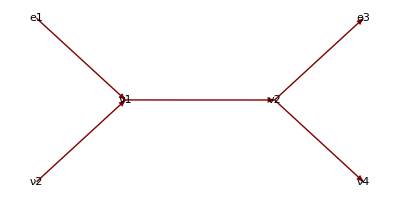

```mathematica
scale=.5
GraphPlot[{{e1->v1,"p1"},{ν2->v1,"p2"},{v1->v2,"Z"},{v2->e3,"p3"},{v2->ν4,"p4"}},DirectedEdges-> True,VertexLabeling->True,VertexCoordinateRules->{e1->{0,scale },ν2->{0,-scale},e3->{4 scale,scale},ν4->{4scale,-scale}}]
```

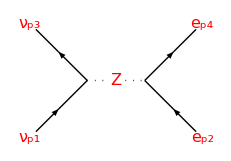

```mathematica
scale=1;
MidArrow[xy_]:={Arrow[{xy[[1]],(xy[[1]]+xy[[2]])/2}],Line[{(xy[[1]]+xy[[2]])/2,xy[[2]]}]
}
TextOver[text_,xy_]:={White,Disk[xy,0.15scale],
Text[Style[text,FontSize->16,Red],xy]}

Graphics[{Thick,Black,
MidArrow[{{0,-scale},{scale,0}}],
MidArrow[{{scale,0},{0,scale}}],
MidArrow[{{3 scale,-scale},{2 scale,0}}],
MidArrow[{{2 scale,0},{3 scale,scale}}],
Dotted,Line[{{scale,0},{2 scale,0}}],
TextOver[Z,{1.5 scale,0}],
TextOver[Subscript[ν, p1],{0,-scale}],
TextOver[Subscript[ν, p3],{0,scale}],
TextOver[Subscript[e, p4],{3 scale,scale}],
TextOver[Subscript[e, p2],{3 scale,-scale}]
}
]
```

```mathematica
tmpD[[1]]
```

ⅈ OverBar[ψ_Diraq].γ_μ^μ UnderBar[∂]_μ[ψ_Diraq]

```mathematica
subD=Subscript[ψ, Diraq]->{{ηd[undotted@α]},{OverBar[χu[dotted@α]]}}
tmp1=Map[xPartialD[#,μ]&,subD]//.xPartialDExpand[{}]
tmp=subD//First;
sub=OverBar[tmp]->ConjugateTranspose[tmp].γu[0]
tmpD[[1]]
%/.sub//.subγ2σ
%/.subD
//
tmp=Map[OverBar[#]&,subD]
tmp=MapAt[#/.OverBar[a_]->ConjugateTranspose[a].γu[0]&,tmp,2]
tmp=tmp/.subBar
subD={tmp1,tmp}
tmpD[[1]]/.subD
/.subγ2σ;
```

ψ_Diraq→{{η_α^α},{OverBar[χ_α^α]}}

UnderBar[∂]_μ[ψ_Diraq]→{{UnderBar[∂]_μ[η_α^α]},{UnderBar[∂]_μ[OverBar[χ_α^α]]}}

OverBar[ψ_Diraq]→(ψ_Diraq)^†.γ_0^0

ⅈ OverBar[ψ_Diraq].γ_μ^μ.UnderBar[∂]_μ[ψ_Diraq]

ⅈ (ψ_Diraq)^†.{{OverBar[σ_μ^μ],0},{0,σ_μ^μ}}.UnderBar[∂]_μ[ψ_Diraq]

ⅈ {{(η_α^α)^* OverBar[σ_μ^μ],OverBar[χ_α^α]^* σ_μ^μ}}.UnderBar[∂]_μ[{{η_α^α},{OverBar[χ_α^α]}}]

```mathematica
tmp=tmpD[[2]];
MatrixForm[%]
ConjugateTranspose[%];
MatrixForm[%];

(tmps=-I (σu[2]/.sPauli))//MatrixForm;
tmp2=tmps.tmp
MatrixForm[%]
(tmp1=Transpose[tmp])//MatrixForm
{tmp1,tmp2}
gDot[tmp1,tmp2]
```

(η_α^α
OverBar[χ_α^α])

χ_(α̇)^(α̇)

MM

{{-OverBar[χ_α^α]},{η_α^α}}

(-OverBar[χ_α^α]
η_α^α)

(η_α^α | OverBar[χ_α^α])

{{{η_α^α,OverBar[χ_α^α]}},{{-OverBar[χ_α^α]},{η_α^α}}}

2 OverBar[χ_α^α].η_α^α

```mathematica
(*NonCommuting Matrix multiply of 2D matrix {{a,b},{c,d}}against a 1D row vector {{e,f}}
*)
NCMatrixVectorMultiply[a_,b_]:=Module[{tmpb=First[b],DEBUG=1,mname="NCMatrixVectorMultiply"},
IfDEBUG[mname,DEBUG>0,{a,tmpb},"{a,tmpb}"];
Map[{xDotVV[#,b]}&,a]
];
(*NonCommuting 2D-2D Matrix multiply.  Outputs undefined function xDot to maintain ordering.*)
Clear[NCMatrixMultiply0]
NCMatrixMultiply0[a_,b_]:=Module[{tmp,tmpb=Transpose[b],DEBUG=1,mname="NCMatrixMultiply0"},
IfDEBUG[mname,DEBUG>0,{a,tmpb},"{a,tmpb}"];
IfDEBUG[mname,DEBUG>0,{First[a],First[tmpb]},"First[{a,tmpb}]"];
tmp=Thread[xDot[{a//First,tmpb//First}]]
(*tmp=tmp//.DotExpand//.simpleDot*)
];

NCMatrixMultiply0x[{{e,h}},{{a,b},{c,d}}];
NCMatrixMultiply0[{{a,b},{c,d}},{{e},{h}}]

xDotVV[a_,b_]:=Apply[Plus,Thread[xDot[a,b]]]
```

NCMatrixMultiply0:{a,tmpb}:{{{a,b},{c,d}},{{e,h}}}

NCMatrixMultiply0:First[{a,tmpb}]:{{a,b},{e,h}}

{xDot[{a,b}],xDot[{e,h}]}

xDot[{{e,h}},{{a,b},{c,d}}]

NCMatrixMultiply:{tmp,Length[tmp]}:{xDot[{{e,h}},{{a,b},{c,d}}],2}

NCMatrixMultiply:{tmp}:{xDot[{{xD$8677133[{1,1,1},e],xD$8677133[{1,1,2},h]}}]}

{{e,h}}

```mathematica
NCMatrixMultiply[{{e},{h}},{{i,j},{k,l}},%]
```

{{xDot[a,e]+xDot[b,h]},{xDot[c,e]+xDot[d,h]}}

NCMatrixMultiply:{a}:{{{e},{h}},{{i,j},{k,l}},{{xDot[a,e]+xDot[b,h]},{xDot[c,e]+xDot[d,h]}}}

{{{{{e}+{i,k}}+{xDot[a,e]+xDot[b,h],xDot[c,e]+xDot[d,h]}},{{{h}+{i,k}}+{xDot[a,e]+xDot[b,h],xDot[c,e]+xDot[d,h]}}}}

```mathematica
tmp={{{a1,b1},{c1,d1}},{{a2,b2},{c2,d2}},{{a3,b3},{c3,d3}}}
Apply[Dot,%]
%//Length
```

{{{a1,b1},{c1,d1}},{{a2,b2},{c2,d2}},{{a3,b3},{c3,d3}}}

{{a3 (a1 a2+b1 c2)+c3 (a1 b2+b1 d2),b3 (a1 a2+b1 c2)+(a1 b2+b1 d2) d3},{a3 (a2 c1+c2 d1)+c3 (b2 c1+d1 d2),b3 (a2 c1+c2 d1)+(b2 c1+d1 d2) d3}}

2

```mathematica
tmp={xD[24,{{a1,b1},{c1,d1}}]xD[21,{{a2,b2},{c2,d2}}]xD[20,{{a3,b3},{c3,d3}}]}/.Times->xDot/.xD[_,a_]->a;

tmp=tmp//First
MM
tmp/.xDot[a__]:>MapIndexed[xD[#2,#1]&,{a},{3}]
Apply[Dot,%]/.Times->Dot/.xD[_,a_]->a;
NCxDotMatrixMultiply1[xdotarg__]:=Module[{tmp=xdotarg,xD,DEBUG=0,mname="NCxDotMatrixMultiply1"},
IfDEBUG[mname,DEBUG>0,{tmp},"{tmp}"];
tmp=First[xDot[MapIndexed[xD[#2,#1]&,{tmp},{3}]]];
IfDEBUG[mname,DEBUG>0,{tmp},"{tmp}"];
Apply[Dot,tmp]/.Times->Dot/.xD[_,a_]->a
];
tmpx
tmp=tmpx/.xDot[a__]:>NCxDotMatrixMultiply1[a]/.simpleDot
```

xDot[{{a3,b3},{c3,d3}},{{a2,b2},{c2,d2}},{{a1,b1},{c1,d1}}]

MM

{{{xD[{1,1,1},a3],xD[{1,1,2},b3]},{xD[{1,2,1},c3],xD[{1,2,2},d3]}},{{xD[{2,1,1},a2],xD[{2,1,2},b2]},{xD[{2,2,1},c2],xD[{2,2,2},d2]}},{{xD[{3,1,1},a1],xD[{3,1,2},b1]},{xD[{3,2,1},c1],xD[{3,2,2},d1]}}}

ⅈ xDot[{{OverBar[η_α^α],χ_α^α}},{{OverBar[σ_μ^μ],0},{0,σ_μ^μ}},{{UnderBar[∂]_μ[η_α^α]},{UnderBar[∂]_μ[OverBar[χ_α^α]]}}]

{{ⅈ (OverBar[η_α^α].OverBar[σ_μ^μ].UnderBar[∂]_μ[η_α^α]+χ_α^α.σ_μ^μ.UnderBar[∂]_μ[OverBar[χ_α^α]])}}